```mathematica
SetDirectory["/Users/arsenytokarev/Desktop/LaTeX/Kursach/Pictures"]
```

/Users/arsenytokarev/Desktop/LaTeX/Kursach/Pictures

```mathematica
constants = {a1= 3, a2= 2.3, b12 =  1, b21 = 1, c1 =  2.2, c2 =  1};
growth = { 
x *(a1 -b12 y - c1 x),
y *(a2 - b21 x - c2  y)
 };
```

```mathematica
stationaryPoints = {{0, 0},{0, a2/c2 },{a1/c1, 0},{(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}};
sss = {"0", "a2/c2","a1/c1",""};
```

```mathematica
labels = Text[#, Offset[{10,10}, #] ] &/@ stationaryPoints;
labels = { 
Text["0", Offset[{10,10}, {0, 0 }]],
Text["a2/c2", Offset[{10,10}, {0, a2/c2 }]],
Text["a1/c1", Offset[{10,10}, {a1/c1, 0}]],
Text["γ_1 ∩ γ_2", Offset[{10,10}, {(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}]]
};
```

## Изоклины

```mathematica
endX = If[a1/b12 > a2/b21, a1/b12, a2/b21 ];
```

```mathematica
endY = If[a1/c1 > a2/c2, a1/c1, a2/c2 ];
```

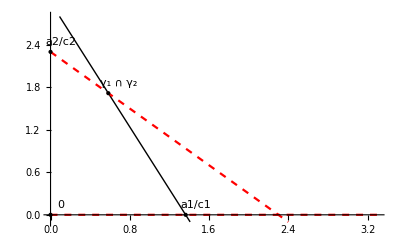

```mathematica
nullclinesPlot = Plot[
{0, (-c1  x + a1)/b12, (a2-b21 x)/c2}, {x, 0,endX + 0.3}, Epilog->{labels,Black,PointSize@Large,Point[stationaryPoints]},
PlotRange->{-0.1,endY  + 0.5},
PlotStyle->{{Dashed, Red},{Thick, Black} }]
```

## Линеаризация

```mathematica
linMatrix = {{a1- b12 y  - 2c1 x, -b12 x},{-b21 y, a2 - b21 x - 2c2 y}};
```

```mathematica
stationaryReplacements={{x-> 0, y-> 0},{x -> 0, y -> a2/c2 },{x -> a1/c1,y -> 0},{x->(a1 c2 - a2 b12)/(c1 c2 - b12 b21),y->(a2 c1-a1 b21)/(c1 c2 - b12 b21)}};
```

## Фазовый портрет

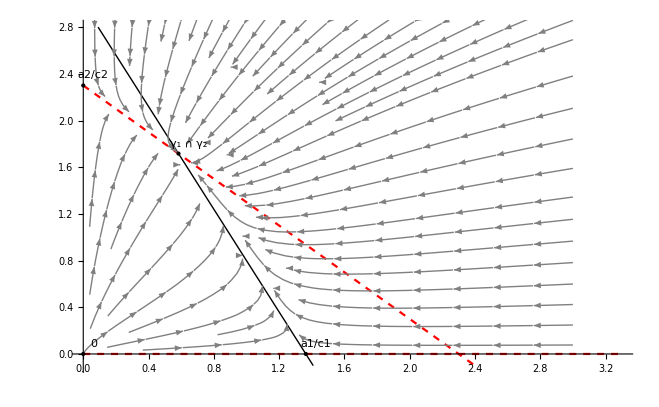

```mathematica
Show[nullclinesPlot,StreamPlot[growth,{x,0,endX},{y,0,5} , StreamStyle-> Gray]]
```

```mathematica
Callout
```

Callout

```mathematica
CompetingSpeciesModel[a1_, b12_, c1_, a2_, b21_, c2_, case_] := Module[
{
stationaryPoints1,stationaryPoints2 ,
labels1, labels2,labels3,
endX,
endY,
nullclinesPlot1, nullclinesPlot2, nullclinesPlot3,
linMatrix,
stationaryReplacements
}, 
stationaryPoints1 = {{0, 0},{0, a2/c2 },{a2/b21, 0 },{a1/c1, 0}, {0, a1/b12},{(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}};
stationaryPoints2 = {{0, 0},{0, a2/c2 },{a1/c1, 0},{(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}};  
labels1 = Text[#,Offset[{10,10},#] ] &/@ stationaryPoints1;
labels2 = Text[#,Offset[{10,10},#] ] &/@ stationaryPoints;
labels1 = { 
Text[Style["0", Medium, 18], Offset[{10,10}, {0, 0 }]],
Text[Style["a_2/c_2", Medium, 18], Offset[{25,15}, {0, a2/c2 }]],
Text[Style["a_2/b_21", Medium, 18], Offset[{25,15}, {a2/b21, 0 }]],
Text[Style["a_1/c_1", Medium, 18], Offset[{25,15}, {a1/c1, 0}]],
Text[Style["a_1/b_12", Medium, 18], Offset[{25,15}, {0, a1/b12}]],
Text[Style["L_1 ∩ L_2", Medium, 18], Offset[{25,15}, {(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}]]
};
labels2 = { 
Text[Style["0", Medium, 18], Offset[{10,10}, {0, 0 }]],
Text[Style["a_2/c_2", Medium, 18], Offset[{25,15}, {0, a2/c2 }]],
Text[Style["a_1/c_1", Medium, 18], Offset[{25,15}, {a1/c1, 0}]],
Text[Style["L_1 ∩ L_2", Medium, 18], Offset[{25,15}, {(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}]]
};
If[case == 
True, 
labels3 = { 
Text[Style["1", Medium, 40], Offset[{80,100}, {0,0 }]],
Text[Style["4", Medium, 40], Offset[{-40,25}, {(a1/c1+a2/b21)/2, 0}]],
Text[Style["2", Medium, 40], Offset[{25,-30}, {0,( a1/b12 + a2/c2)/2}]],
Text[Style["3", Medium, 40], Offset[{100,100}, {(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}]]
},
labels3 = { 
Text[Style["1", Medium, 40], Offset[{30,30}, {0,0 }]],
Text[Style["2", Medium, 40], Offset[{80,150}, {0,0 }]],
Text[Style["3", Medium, 40], Offset[{0,200}, {a1/c1, 0}]]
}
];

endX = If[a1/b12 > a2/b21, a1/b12, a2/b21 ];
endY = If[a1/c1 > a2/c2, a1/c1, a2/c2 ];
nullclinesPlot1 = Plot[
{0, (-c1  x + a1)/b12, (a2-b21 x)/c2}, {x, 0,endX + 0.1}, 
Epilog->{labels1,Black,PointSize@Large,Point[stationaryPoints1]},
PlotRange->{-0.1,endY + 1 },
AxesLabel->{Style["x_1",Medium,18],Style["x_2",Medium,18]},
Ticks->False,
 PlotLegends->{Style["L_1: (a_2 - b_21 x_1) / c_2 , \n\nx_2= 0 \n\n\n", Medium, 22],Style["L_2: (-c_1x_1 + a_1) / b_12 ,\n\nx_1 = 0", Medium, 22]},
AxesStyle->{Black,Black},
LabelStyle->{FontFamily->"Helvetica",14},ImageSize->600,AspectRatio->Full,
PlotStyle->{{Dashed, Black},{Thick, Black, Thickness[0.002]} }];
linMatrix = {{a1- b12 y  - 2c1 x, -b12 x},{-b21 y, a2 - b21 x - 2c2 y}};stationaryReplacements={{x-> 0, y-> 0},{x -> 0, y -> a2/c2 },{x -> a1/c1,y -> 0},{x->(a1 c2 - a2 b12)/(c1 c2 - b12 b21),y->(a2 c1-a1 b21)/(c1 c2 - b12 b21)}};
nullclinesPlot2 = Plot[
{0, (-c1  x + a1)/b12, (a2-b21 x)/c2}, {x, 0,endX }, 
Epilog->{labels2,Black,PointSize@Large,Point[stationaryPoints2]},
PlotRange->{-0.1,endY + 0.4},
AxesLabel->{Style["x_1",Medium,18],Style["x_2",Medium,18]},
Ticks->False,
AxesStyle->{Black,Black},
LabelStyle->{FontFamily->"Helvetica",14},ImageSize->600,AspectRatio->Full,
PlotStyle->{{Dashed, Black},{Thick, Black, Thickness[0.002]} }];
nullclinesPlot3= Plot[
{0, (-c1  x + a1)/b12, (a2-b21 x)/c2}, {x, 0,endX }, 
Epilog->{labels3,Black,PointSize@Large,Point[stationaryPoints2]},
PlotRange->{-0.1,endY + 0.4},
AxesLabel->{Style["x_1",Medium,18],Style["x_2",Medium,18]},
Ticks->False,
AxesStyle->{Black,Black},
LabelStyle->{FontFamily->"Helvetica",14},ImageSize->600,AspectRatio->Full,
PlotStyle->{{Dashed, Black},{Thick, Black, Thickness[0.002]} }
];
{
Show[nullclinesPlot2, StreamPlot[{ x *(a1 -b12 y - c1 x),y *(a2 - b21 x - c2  y)},{x,0,endX},{y,0,endY +2} ,StreamStyle-> GrayLevel[0.4], StreamScale -> Tiny],nullclinesPlot2], 
nullclinesPlot1,
Show[nullclinesPlot3, VectorPlot[{ x *(a1 -b12 y - c1 x),y *(a2 - b21 x - c2  y)},{x,0,endX},{y,0,endY +2}, VectorMarkers-> "Arrow",VectorStyle->GrayLevel[0.5], VectorColorFunction->Black]],
Show[nullclinesPlot3, VectorPlot[{ 1, x *(a1 -b12 y - c1 x)},{x,0,endX},{y,0,endY +2}, VectorMarkers-> "Arrow",VectorStyle->GrayLevel[0.5], VectorColorFunction->Black]],
Show[nullclinesPlot3, VectorPlot[{ 1, y *(a2 - b21 x - c2  y)},{x,0,endX},{y,0,endY +2}, VectorMarkers-> "Arrow",VectorStyle->GrayLevel[0.5], VectorColorFunction->Black]]
}
]
```

```mathematica
(*Manipulate[CompetingSpeciesModel[a1,b12,c1,a2,b21,c2], {{a1,3,"Размножение I" }, 0.1, 20, 0.2},{{b12,2, "Межвидовая I"}, 1,20, 0.5},{{c1,2, "Внутривидовая I"}, 1, 20, 0.5},{{a2,5, "Разможение II"}, 0.1, 20, 0.2},{{b21,1,"Межвидовая II" }, 1, 20, 0.5},{{c2,1, "Внутривидовая II"}, 1, 20, 0.5}]*)
```

```mathematica
exportPlot1 = CompetingSpeciesModel[3, 1, 2.2, 2.3, 1, 1, True];
```

```mathematica
exportPlot2 = CompetingSpeciesModel[4, 2, 2.5, 2.7, 2.5, 1 , True];
```

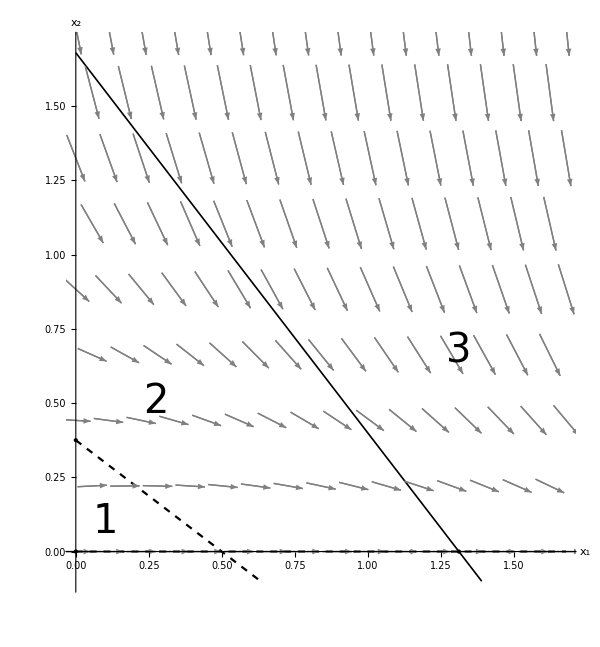

```mathematica
exportPlot3[[4]]
```

```mathematica
Export["sep_1.pdf", exportPlot1[[2]], ImageResolution->1000];
Export["sep_2.pdf", exportPlot2[[2]], ImageResolution->1000];
```

```mathematica
Export["phase_1.pdf", exportPlot1[[1]], ImageResolution->1000];
Export["phase_2.pdf", exportPlot2[[1]], ImageResolution->1000];
```

```mathematica
Export["areas_1.pdf", exportPlot1[[3]], ImageResolution->1000];
Export["areas_2.pdf", exportPlot2[[3]], ImageResolution->1000];
Export["dirFields_11.pdf", exportPlot1[[4]], ImageResolution->1000];
Export["dirFields_21.pdf", exportPlot2[[4]], ImageResolution->1000];
Export["dirFields_12.pdf", exportPlot1[[5]], ImageResolution->1000];
Export["dirFields_22.pdf", exportPlot2[[5]], ImageResolution->1000];
```

```mathematica
exportPlot3 = CompetingSpeciesModel[4.2, 2.5, 3.2, 0.75, 1.5, 2 , False];
```

```mathematica
exportPlot4 = CompetingSpeciesModel[5.3, 4, 2, 5, 1, 1  , False];
```

```mathematica
Export["sep_3.pdf", exportPlot3[[2]], ImageResolution->1000];
Export["sep_4.pdf", exportPlot4[[2]], ImageResolution->1000];
```

```mathematica
Export["phase_3.pdf", exportPlot3[[1]], ImageResolution->1000];
Export["phase_4.pdf", exportPlot4[[1]], ImageResolution->1000];
```

```mathematica
Export["areas_3.pdf", exportPlot3[[3]], ImageResolution->1000];
Export["areas_4.pdf", exportPlot4[[3]], ImageResolution->1000];
```

```mathematica
Export["dirFields_31.pdf", exportPlot3[[4]], ImageResolution->1000];
Export["dirFields_41.pdf", exportPlot4[[4]], ImageResolution->1000];
Export["dirFields_32.pdf", exportPlot3[[5]], ImageResolution->1000];
Export["dirFields_42.pdf", exportPlot4[[5]], ImageResolution->1000];
```